# Initialisation

fixed parameters

```mathematica
ClearAll[Ip,ω,r]
Ip=0.5;
ω = 0.057;
r={π/4,π/4.5,π/5,π/5.5,π/6,π/6.5,π/7,π/7.5,π/8,π/8.5,π/9,π/9.5,π/10,π/10.5,π/11,π/11.5,π/12}
```

{π/4,0.698132,π/5,0.571199,π/6,0.483322,π/7,0.418879,π/8,0.369599,π/9,0.330694,π/10,0.299199,π/11,0.273182,π/12}

function definitions

```mathematica
ClearAll[E1,A, Sf,Sfunc, DsFunc]
(*Define the electric field function and the vector potential*)
E1[t_,k_]:=Cos[k] Cos[t]-Sin[k] Cos[2t];
A[tx_,k_]=-Integrate[E1[t,k],t]/. t->tx;

(*Define Sf,Sfunc,and DsFunc*)
Sf[ty_,p_,k_]=Integrate[2 p*A[t,k]+(A[t,k])^2,t]/. t->ty;
Sfunc[t_,p_,k_]:=0.5*Sf[t,p,k]+(0.5*p^2+Ip)*t;
DsFunc[t_,p_,k_]:=D[Sfunc[tz,p,k],tz]/. tz->t;
```

define momentum grid

```mathematica
ClearAll[pxValues]
(*Define the range for px and py values*)
pxValues=Range[-3,3,0.1];
Print[Length[pxValues]]
```

61

define plotting functions

```mathematica
ClearAll[plotEx,plotRoots](*Plot Ex  and roots*)
plotEx[k_]:=Quiet[Plot[E1[t,k],{t,realMin,realMax},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]]

plotRoots[filteredTValues_,k_]:=Quiet[ListPlot[{{Re[#],E1[Re[#],k][[1]]}&/@filteredTValues},PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]];
```

create grid of seeds

```mathematica
ClearAll[realMax,realMin,imagMax,imagMin,realSteps,imagSteps,listofseeds,initialGuess,listofseeds,seedPoints](*Generate the grid of seeds*) 

(*pick realmin to realmax as the range to capture the 4 saddle points in a periodic range of 2Pi*)
realMin=-2.133;realMax=4.150;
imagMin=0;imagMax=5;
realSteps=10;imagSteps=10;

listofseeds=Flatten[Table[x+I y,{x,realMin,realMax,(realMax-realMin)/realSteps},{y,imagMin,imagMax,(imagMax-imagMin)/imagSteps}],1];
```

find all the roots for all values of px (saddle point solutions)

```mathematica
ClearAll[generatePlotAndRoots];

(*Function to generate plots and roots for a given p*)
generatePlotAndRoots[p_,k_]:=
Module[
{allSolutions,complexSolutions,nonrepeatedSolutions,tValues,tolerance,filteredTValues},

(*Find roots*)
allSolutions=Round[t/. Quiet[
Table[
FindRoot[DsFunc[t,p,k]==0,{t,tseed}],
{tseed,listofseeds}]
],0.0001];

complexSolutions=Select[allSolutions,Im[#]>0&];
nonrepeatedSolutions=DeleteDuplicates[complexSolutions];
tValues=SortBy[Select[nonrepeatedSolutions,(Re[#]>=realMin&&Re[#]<=realMax)&],Re[#]&];

(*Define a tolerance for considering values as 0*)
tolerance=10^-3;
filteredTValues=Select[tValues,Abs[Re[DsFunc[#,p,k]]]<=tolerance&&Abs[Im[DsFunc[#,p,k]]]<=tolerance&];

(*Return both the plot and filteredTValues*)
{filteredTValues}];
```

# Calculation of saddle point solutions!

```mathematica
(*Generate results using the precise pValues*)
results=Table[Table[
generatePlotAndRoots[p,r[[i]]],{p,pxValues}
],{i,Length[r]}]
```

```mathematica
Print[Length[results]]
Print[Length[pxValues]]
Print[Length[r]]
```

17

61

17

# Rearranging data structure for time arrays

```mathematica
ClearAll[newResults,tsExtended,validData,realAndImagTimes,colorFunction,coloredPoints];

newResults=Table[Table[
{pValue=-3+(i-1)*0.1,results[[q,i,1]]},
{i,Length[results[[q]]]}
],{q,Length[r]}];

tsExtended=Table[Map[
Join[
{#[[1]]},PadRight[#[[2]],4,Null]
]&,newResults[[q]]],{q,Length[r]}];

(*Filter and prepare the data for further processing*)
validData=Table[Select[
Flatten[
Table[
If[
tsExtended[[q,i,j+1]]=!=Null,
{Re[tsExtended[[q,i,j+1]]],Im[tsExtended[[q,i,j+1]]],tsExtended[[q,i,1]]},
Nothing],
{i,Length[tsExtended[[q]]]},
{j,1,4}]
,1],
#[[1]]=!=Null&],{q,Length[r]}];

(*Extract real and imaginary times*)
realAndImagTimes=Table[validData[[q,All,1;;2]],{q,Length[r]}];

colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Generate a list of colored points with the custom color function*)
coloredPoints=
Table[
Table[

{colorFunction[validData[[q,i,3]]]
,Point[validData[[q,i,1;;2]]]
}
,{i,1,Length[validData[[q]]]}]
,{q,Length[r]}];
```

# plotting saddle points complex plane (px rainbow scale)

```mathematica
(*Plot the 2D graph*)
Manipulate[
ListPlot[
realAndImagTimes[[q]],

AxesLabel->{"Real Time","Imaginary Time"},
PlotStyle->PointSize[Medium],
GridLines->Automatic,
ImageSize->Medium,PlotRange->All]
,
{{q,1,"Index"},1,Length[r],1}]

(*Plot the 2D graph with the custom color grading for momentum*)
Manipulate[
Show[
Graphics[
{coloredPoints[[q]]},

Axes->True,
AxesLabel->{"Real Time","Imaginary Time"},
GridLines->Automatic],
PlotRange->All,
ImageSize->Medium,
AspectRatio->1/GoldenRatio],
{{q,1,"Index"},1,Length[r],1}]
```

# Calculating & plotting 2D real trajectories inside the tunnel (ReX vs ReT)

define X first (Ideally calculate X traj first then plot)

```mathematica
X1[t_,p_,k_]=Evaluate[Integrate[p+A[t,k],t]];
X[t_,p_,ts_,k_]:=X1[t,p,k]-X1[ts,p,k];
(*Real trajectory vs Imaginary time*)

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]
```

and then plot stuff

```mathematica
ClearAll[fixedPlotRange,imaginaryPlots, combinedImaginaryPlots];
(*Define a fixed plot range for comparison*)
fixedPlotRange={{0,2.5},{-2,1}}; 

(*Collect individual plots for each saddle point*)
imaginaryPlots=
Table[
Table[
Module[
{p=tsExtended[[q,k,1]]},
Plot[Re[X[Re[tsExtended[[q,k,i]]]+I ti,p,tsExtended[[q,k,i]],r[[q]]]],
{ti,Im[tsExtended[[q,k,i]]],0},

PlotRange->(*All*)fixedPlotRange,
AxesLabel->{"Im[t]","Re[X[t]]"},
PlotStyle->{Thick,colorFunction[p]},
PlotLabel->"p = "<>ToString[p],
ImageSize->Large]
],
{k,1,Length[tsExtended[[q]]]},{i,2,5}]
,{q,Length[r]}];

(*Combine plots for each saddle point*)
combinedImaginaryPlots=
Table[
Table[
Show[
imaginaryPlots[[q,All,i]],

PlotRange->(*All*)fixedPlotRange,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}],{q,Length[r]}];
```

```mathematica
(*Export["2dtraj1.mp4",combinedImaginaryPlots,"FrameRate"->0.5]*)
```

2dtraj1.mp4

# Calculating & plotting 3D real trajectories inside & outside the tunnel (ReX vs ImT vs ReT)

```mathematica
ClearAll[threeDPlots,combinedThreeDPlots];
(*3D plot of the whole trajectory inside and outside the tunnel, ReX vs ReT vs ImT*)
(*Collect individual plots for each saddle point*)
threeDPlots=
Table[
Table[
Module[
{p=tsExtended[[q,k,1]]},

Show[
{ParametricPlot3D[
{Re[tr+I ti],Im[tr+I ti],Re[X[tr+I ti,p,tsExtended[[k,i]],r[[q]]]]}
/. tr->Re[tsExtended[[q,k,i]]],
{ti,Im[tsExtended[[q,k,i]]],0},

PlotRange->All,
AxesLabel->{"Re[t]","Im[t]","Re[X[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]],

ParametricPlot3D[
{Re[tr+I ti],Im[tr+I ti],Re[X[tr+I ti,p,tsExtended[[k,i]],r[[q]]]]}
/. ti->0.,
{tr,Re[tsExtended[[q,k,i]]],Re[tsExtended[[q,k,i]]]+2 Pi},

PlotRange->All,
AxesLabel->{"Re[t]","Im[t]","Re[X[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]]}]
],{k,1,Length[tsExtended[[q]]]},{i,2,5}],{q,Length[r]}];

(*Combine plots for each saddle point*)
combinedThreeDPlots=
Table[
Table[
Show[
threeDPlots[[q,All,i]],

PlotRange-> All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}],{q,Length[r]}];

(*(*Display combined plots*)
combinedThreeDPlots*)
```

Part::partd: Part specification threeDPlots⟦1,All,1⟧ is longer than depth of object.

Show::gtype: Part is not a type of graphics.

Part::partd: Part specification threeDPlots⟦1,All,2⟧ is longer than depth of object.

Show::gtype: Part is not a type of graphics.

Part::partd: Part specification threeDPlots⟦1,All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gtype: Part is not a type of graphics.

General::stop: Further output of Show::gtype will be suppressed during this calculation.

$Aborted

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

# Calculating & plotting 3D real & imaginary trajectories inside the tunnel (ReX vs ImX vs ImT)

```mathematica
X1[t_,p_,k_]=Evaluate[Integrate[p+A[t,k],t]];
X[t_,p_,ts_,k_]:=X1[t,p,k]-X1[ts,p,k];
(*Real trajectory vs Imaginary time*)

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]
```

```mathematica
ClearAll[threeDPlots2,combinedThreeDPlots2];

(*3D plot of real and imaginary trajectories against imaginary time*)
(*Collect individual plots for each saddle point*)
threeDPlots2=
Table[Table[
Module[
{p=tsExtended[[q,k,1]]},

Show[
{ParametricPlot3D[
{Im[tr+I ti],Im[X[tr+I ti,p,tsExtended[[q,k,i]],r[[q]]]],Re[X[tr+I ti,p,tsExtended[[q,k,i]],r[[q]] ]]}
/. tr->Re[tsExtended[[q,k,i]]],
{ti,Im[tsExtended[[q,k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Im[X[t]]","Re[X[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]]}
]],{k,1,Length[tsExtended[[q]]]},{i,2,5}],{q,Length[r]}];

(*Combine plots for each saddle point*)
combinedThreeDPlots2=
Table[Table[
Show[
threeDPlots2[[q,All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}],{q,Length[r]}];

(*Display combined plots*)
(*combinedThreeDPlots2*)
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Show[%,PlotRange-> All]
```

-Graphics3D-

# EXTRA: 2D&3D Plots Velocity, Electric field trajectories inside tunnel

## Calculating & plotting 2D real velocities inside the tunnel (ReV vs ImT)

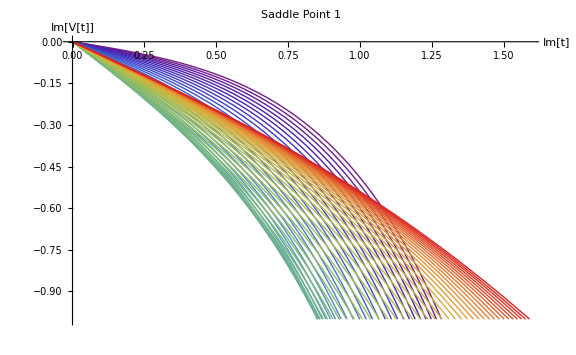
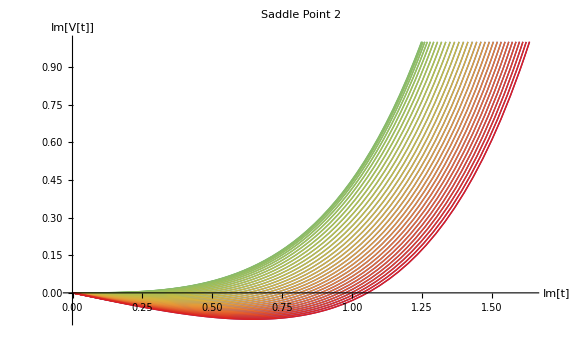
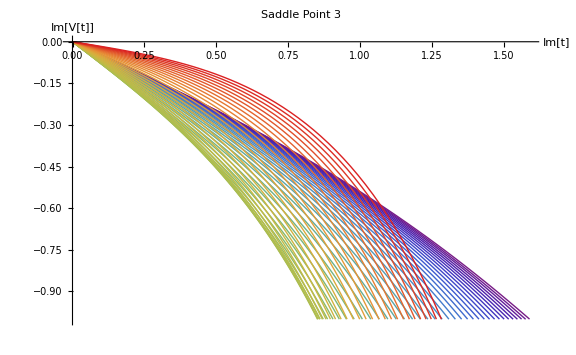
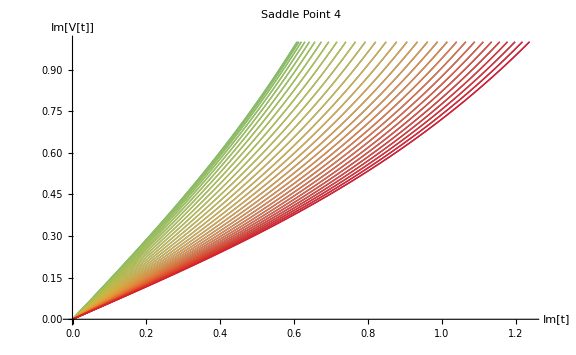

```mathematica
ClearAll[V1,imaginaryPlots2, combinedImaginaryPlots2];
(*Imaginary Velocity vs Imaginary time*)
V1[t_,p_]:=p+A[t];

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Collect individual plots for each saddle point*)
imaginaryPlots2=
Table[
Module[
{p=tsExtended[[k,1]]},
Plot[Im[V1[Re[tsExtended[[k,i]]]+I ti,p]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Im[V[t]]"},
PlotStyle->{Thick,colorFunction[p]},
PlotLabel->"p = "<>ToString[p]]
],
{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedImaginaryPlots2=
Table[
Show[
imaginaryPlots2[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)

combinedImaginaryPlots2
```

## Calculating & plotting 3D real & imaginary velocities inside the tunnel (ReV vs ImV vs ImT)

```mathematica
(*3D plot of real and imaginary velocities against imaginary time*)

ClearAll[V1,threeDPlots2, combinedThreeDPlots2];

V1[t_,p_]:=p+A[t];

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Collect individual plots for each saddle point*)
threeDPlots2=
Table[
Module[
{p=tsExtended[[k,1]]},

Show[
{ParametricPlot3D[
{Im[tr+I ti],Im[V1[tr+I ti,p]],Re[V1[tr+I ti,p]]}
/. tr->Re[tsExtended[[k,i]]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Im[V[t]]","Re[V[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]]}
]],{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedThreeDPlots2=
Table[
Show[
threeDPlots2[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)
combinedThreeDPlots2
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Show[%,PlotRange-> All]
```

-Graphics3D-

## Calculating & plotting 2D real electric field inside the tunnel (ReE1 vs ImT)

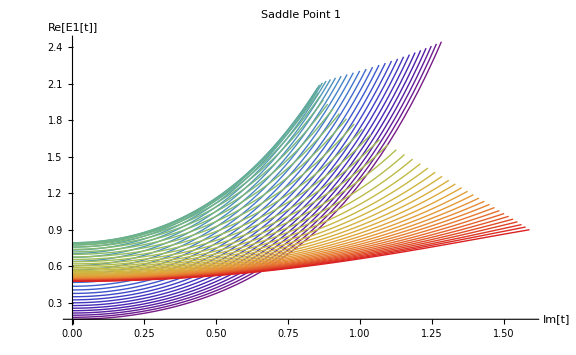
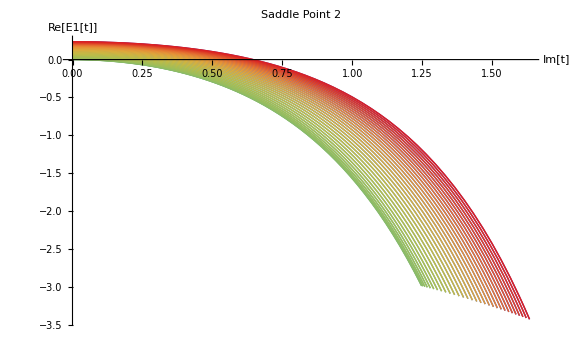
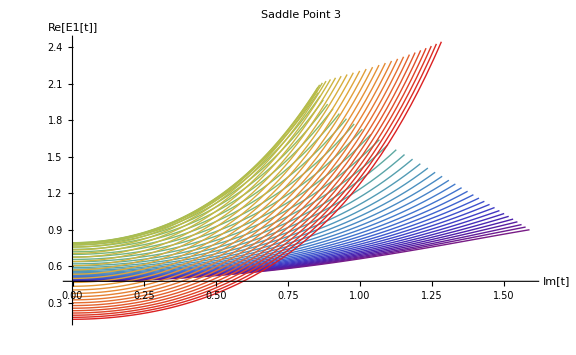
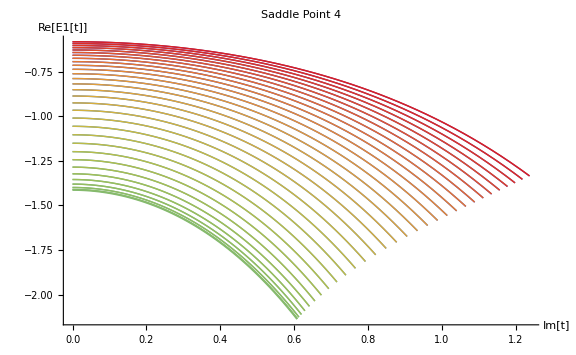

```mathematica
(*Real Electric field for all saddle points (with different moment p) against imaginary time.*)

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Collect individual plots for each saddle point*)
imaginaryPlots1=
Table[
Module[
{p=tsExtended[[k,1]]},
Plot[
Re[E1[Re[tsExtended[[k,i]]]+I ti]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Re[E1[t]]"},
PlotStyle->{Thick,colorFunction[p]},
PlotLabel->"p = "<>ToString[p]]
],
{k,1,Length[tsExtended]},{i,2,5}
];

(*Combine plots for each saddle point*)
combinedImaginaryPlots1=
Table[
Show[
imaginaryPlots1[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large
],
{i,1,4}
];

(*Display combined plots*)
combinedImaginaryPlots1
```

## Calculating & plotting 3D real & imaginary electric field inside the tunnel (ReE1 vs ImE1 vs ImT)

```mathematica
(*3D plot of real and imaginary electric field against imaginary time*)
ClearAll[threeDPlots3, combinedThreeDPlots3];

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Collect individual plots for each saddle point*)
threeDPlots3=
Table[
Module[
{p=tsExtended[[k,1]]},

Show[
{ParametricPlot3D[
{Im[tr+I ti],Im[E1[Re[tsExtended[[k,i]]]+I ti]],Re[E1[Re[tsExtended[[k,i]]]+I ti]]}
/. tr->Re[tsExtended[[k,i]]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Im[E1[t]]","Re[E1[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]]}
]],{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedThreeDPlots3=
Table[
Show[
threeDPlots3[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)
combinedThreeDPlots3
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Show[%,PlotRange->All]
```

-Graphics3D-